# Rule(→)

```mathematica
{x,x^2,a,b}/.x->3   (*Replace x by 3*)
```

{3,9,a,b}

```mathematica
Rule1=x^n_->f[n]
```

x^n_→f[n]

```mathematica
1+f[x]+f[y]/.f[x]->p
```

1+p+f[y]

```mathematica
{x,x^2,x^3,a,b}/.Rule1
```

{x,f[2],f[3],a,b}

```mathematica
{x,x,x}/.x-> RandomReal[]
```

{0.0629759,0.0629759,0.0629759}

```mathematica
1+f[x]+f[y]/.f[x_]->x^2
```

1+x^2+y^2

```mathematica
{1,3,2,x,6,Pi}/._Integer:>"int" (*Replace expressions with a particular head*)
```

{int,int,int,x,int,π}

```mathematica
a+x^2+y^6/.{x->2+a,a->1}
```

1.84626+y^6

# RuleDelayed(:>)

```mathematica
{x,x,x}/.x:>  RandomReal[] (*The right-hand side is evaluated separately each time it is used*)
```

{0.0770168,0.101956,0.811783}

# ReplaceRepeated(//.)

```mathematica
Rule2={Log[x_ y_]:>   Log[x]+Log[y],Log[x_^k_]:>  k Log[x]};
```

```mathematica
Log[x^2 y]/.Rule2
```

Log[x^2]+Log[y]

```mathematica
Log[x^2 y]//.Rule2 (*Apply rules for the power and product laws for logarithms of real numbers recursively*)
```

2 Log[x]+Log[y]

```mathematica
{f[1],f[1,f[1,2]],f[1,f[1,2,3]]}//.f[1,x_Integer]:>1
```

{f[1],1,f[1,f[1,2,3]]}

# Condition(/;)

```mathematica
{6,-7,3,2,-1,-2}/.x_/;x<0->w (*Replace all elements which satisfy the condition of being negative*)
```

{6,w,3,2,w,w}

```mathematica
f[x_]:=ppp[x]/;x>0 (*Make a definition with the condition that x should be positive*)
```

```mathematica
f[2]
```

ppp[2]

```mathematica
f[0]
```

f[0]

# SetDelayed or DefineFunction (:=)

```mathematica
r:=RandomReal[] (*A variable defined with SetDelayed is evaluated every time it is used:*)
```

```mathematica
{r,r,r}
```

{0.627271,0.425519,0.747903}

```mathematica
x=RandomReal[]; (*The right side of an immediate definition is evaluated when the definition is made:*)
{x,x,x}
```

{0.392951,0.392951,0.392951}

```mathematica
fact[1]=1;
fact[n_]:=n fact[n-1]
```

```mathematica
fact[10]
```

3628800

```mathematica
g[x_/;x>0]:=Sqrt[2 x]
```

```mathematica
{g[2],g[-2]}
```

{2,g[-2]}

```mathematica
G[x_Integer]:=Prime[x]-x (*Prime[x] is the prime number of order x*)
```

```mathematica
{G[6],G[z]}
```

{7,G[z]}

# Alternatives(|)

```mathematica
{a,b,c,d,a,b,b,b}/.a|b->x (*Replace instances of either a or b*)
```

{0.919924,0.919924,c,d,0.919924,0.919924,0.919924,0.919924}

```mathematica
F[x_Integer|x_Real]:=x^2
```

```mathematica
F[a]
```

F[a]

```mathematica
x
```

0.392951

```mathematica
ClearAll["`*"] (*Clear all symbols in the current context*)
```

```mathematica
x
```

x

```mathematica
F[2]
```

F[2]

# Others

```mathematica
ySeries=Series[y[t+h],{h,0,3}];
```

```mathematica
yRule=Derivative[k_][y][t]:>  D[f[y[t]],{t,k-1}];
```

```mathematica
ySeries//.yRule
```

y[t]+f[y[t]] h+1/2 f[y[t]] f'[y[t]] h^2+1/6 (f[y[t]] f'[y[t]]^2+f[y[t]]^2 f''[y[t]]) h^3+O[h]^4

```mathematica
Y[t_] = Table[Subscript[y,k][t],{k,1,3}]
```

{y_1[t],y_2[t],y_3[t]}

```mathematica
L[(y[t+h/2]+y[t-h/2])/2,(y[t+h/2]-y[t-h/2])/h]
```

```mathematica
Flatten[{{a,b},{c,{d},e},{f,{g,h}}}]
```

{a,b,c,d,e,f,g,h}

```mathematica
Prime[5]
```

11

# Work with Solution

```mathematica
sol=Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

```mathematica
sol[[1]]
```

{x→1/2 (-a-√(-4+a^2))}

```mathematica
x+4/. sol[[1]]
```

4+1/2 (-a-√(-4+a^2))

# DSolve

```mathematica
eqn={y''[x]+4 y[x]==7,y[0]==1,y'[0]==2}; (*ODE*)
sol1=DSolve[eqn,y[x],x]
```

{{y[x]→1/4 (7-3 Cos[2 x]+4 Sin[2 x])}}

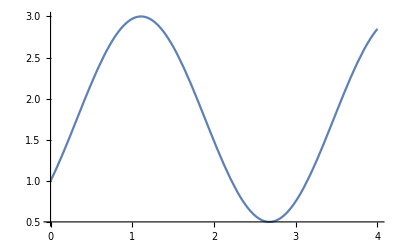

```mathematica
Plot[{y[x]/.sol1},{x,0,4}] (*Plot the solution of ODE*)
```

```mathematica
F[t_]=y[t]/.First@DSolve[{y''[t]+4 y[t]==7,y[0]==1,y'[0]==2},y,t]
```

1/4 (7-3 Cos[2 t]+4 Sin[2 t])

```mathematica
eqns={y'[x]==y[x]-a z[x],z'[x]==y[x]-z[x],y[0]==1,z[0]==4};  (*System ODEs*)
sol2=DSolve[eqns,{y,z},x]
```

{{y→Function[{x},(ⅇ^(-√(1-a) x) (-1+√(1-a)+4 a+ⅇ^(2 √(1-a) x)+√(1-a) ⅇ^(2 √(1-a) x)-4 a ⅇ^(2 √(1-a) x)))/(2 √(1-a))],z→Function[{x},(ⅇ^(-√(1-a) x) (3+4 √(1-a)-3 ⅇ^(2 √(1-a) x)+4 √(1-a) ⅇ^(2 √(1-a) x)))/(2 √(1-a))]}}

```mathematica
eqns/.sol2//Simplify (*Verify the solution*)
```

{{True,True,True,True}}

# Assumptions and Assuming

```mathematica
$Assumptions=a>0; (*Set global assumptions*)
∫_0^1 x^aⅆx
```

1/(1+a)

```mathematica
Assuming[b>0,∫_0^1 x^bⅆx] (*set up assumptions to be used by functions inside*)
```

1/(1+b)

# Derivative

```mathematica
ClearAll[p0,p1]
```

```mathematica
f[x_]:=Sin[x]+x^2;
```

```mathematica
Derivative[1][f][x]
```

2 x+Cos[x]

## Map(/@)

```mathematica
Map[y,{a,b,c,d,e}] (*Evaluate f on each element of a list*)
```

{y[a],y[b],y[c],y[d],y[e]}

```mathematica
y/@{a,b,c,d,e}(*Shorthand notation of Map*)
```

{y[a],y[b],y[c],y[d],y[e]}

```mathematica
Apply[f,{1,2,4,6,5,8}]
```

f[1,2,4,6,5,8]

```mathematica
f@@{a,b,c,d,e} (*Shorthand notation of Apply*)
```

f[a,b,c,d,e]

## Pure Function

```mathematica
g=(#1+#2)&
```

#1+#2&

```mathematica
g[3,4]
```

7

```mathematica
(Exp[#]+1)&[50]
```

1+ⅇ^50

```mathematica
{#2,1+#1,#1+#2}&[a,b]
```

{b,1+a,a+b}

```mathematica
f[##]&[a,b,c,d]
```

f[a,b,c,d]

## List and Table

```mathematica
Table[i^2,{i,0,20,2}]
```

{0,4,16,36,64,100,144,196,256,324,400}

```mathematica
Table[u[i],{i,0,20,2}]
```

{u[0],u[2],u[4],u[6],u[8],u[10],u[12],u[14],u[16],u[18],u[20]}

```mathematica
Table[i,{i,0,20}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
m=RandomInteger[10,{4,3}]
```

{{0,6,5},{0,6,5},{5,0,7},{10,4,4}}

```mathematica
First@m (*Shorthand notation of First[m]*)
```

{0,6,5}

```mathematica
m// First
```

{0,6,5}

```mathematica
Flatten[m]
```

{0,6,5,0,6,5,5,0,7,10,4,4}

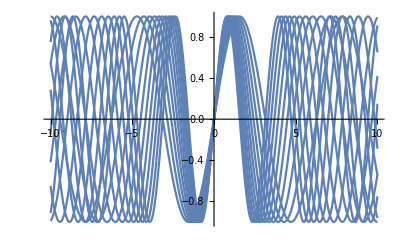

```mathematica
Plot[Table[Sin[a x],{a,1,2,0.1}],{x,-10,10}]
```